```mathematica
R2 = 2*R1;
```

```mathematica
R3 = 3*R1;
```

```mathematica
ZC1 =1/( j*w*C1);
```

```mathematica
Z23 = R2+R3+R2*R3/ZC1
```

3 R1+R2+3 C1 j R1 R2 w

```mathematica
Z2C1 = R2+ZC1+R2*ZC1/R3
```

R2+1/(C1 j w)+R2/(3 C1 j R1 w)

```mathematica
Z3C1 = R3+ZC1+R3*ZC1/R2
```

3 R1+1/(C1 j w)+(3 R1)/(C1 j R2 w)

```mathematica
ZA = ((Z3C1+Z23)*Z2C1)/((Z3C1+Z23)+Z2C1)
```

((R2+1/(C1 j w)+R2/(3 C1 j R1 w)) (6 R1+R2+1/(C1 j w)+(3 R1)/(C1 j R2 w)+3 C1 j R1 R2 w))/(6 R1+2 R2+2/(C1 j w)+(3 R1)/(C1 j R2 w)+R2/(3 C1 j R1 w)+3 C1 j R1 R2 w)

```mathematica
Z04=R1+ZA*ZC1/(ZA+ZC1)
```

R1+((R2+1/(C1 j w)+R2/(3 C1 j R1 w)) (6 R1+R2+1/(C1 j w)+(3 R1)/(C1 j R2 w)+3 C1 j R1 R2 w))/(C1 j w (6 R1+2 R2+2/(C1 j w)+(3 R1)/(C1 j R2 w)+R2/(3 C1 j R1 w)+3 C1 j R1 R2 w) (1/(C1 j w)+((R2+1/(C1 j w)+R2/(3 C1 j R1 w)) (6 R1+R2+1/(C1 j w)+(3 R1)/(C1 j R2 w)+3 C1 j R1 R2 w))/(6 R1+2 R2+2/(C1 j w)+(3 R1)/(C1 j R2 w)+R2/(3 C1 j R1 w)+3 C1 j R1 R2 w)))

```mathematica
Zavar  = Simplify[Z04]
```

(1+2 C1 j R1 w+C1 j R2 w+C1^2 j^2 R1 R2 w^2)/(2 C1 j w+C1^2 j^2 R2 w^2)

```mathematica
I041 = Ux/Zavar
```

(Ux (2 C1 j w+C1^2 j^2 R2 w^2))/(1+2 C1 j R1 w+C1 j R2 w+C1^2 j^2 R1 R2 w^2)

```mathematica
UA = Simplify[I041*ZA*ZC1/(ZA+ZC1)]
```

(Ux+C1 j R2 Ux w)/(1+C1 j (2 R1+R2) w+C1^2 j^2 R1 R2 w^2)

```mathematica
IA = UA*(Z3C1 + Z23)/(Z3C1*Z23)
```

((6 R1+R2+1/(C1 j w)+(3 R1)/(C1 j R2 w)+3 C1 j R1 R2 w) (Ux+C1 j R2 Ux w))/((3 R1+1/(C1 j w)+(3 R1)/(C1 j R2 w)) (3 R1+R2+3 C1 j R1 R2 w) (1+C1 j (2 R1+R2) w+C1^2 j^2 R1 R2 w^2))

```mathematica
Simplify[IA]
```

(Ux (1+2 C1 j R1 w)^2)/(R1 (5+6 C1 j R1 w) (1+4 C1 j R1 w+2 C1^2 j^2 R1^2 w^2))

```mathematica
U04y=IA*Z23
```

((6 R1+R2+1/(C1 j w)+(3 R1)/(C1 j R2 w)+3 C1 j R1 R2 w) (Ux+C1 j R2 Ux w))/((3 R1+1/(C1 j w)+(3 R1)/(C1 j R2 w)) (1+C1 j (2 R1+R2) w+C1^2 j^2 R1 R2 w^2))

```mathematica
Uy = Simplify[U04y]
```

(Ux (1+C1 j R2 w)^2)/(1+C1 j (2 R1+R2) w+C1^2 j^2 R1 R2 w^2)

```mathematica
Gu= Uy/Ux
```

(1+C1 j R2 w)^2/(1+C1 j (2 R1+R2) w+C1^2 j^2 R1 R2 w^2)

```mathematica
Expand[(1+2 C1 j R1 w)^2]
```

1+4 C1 j R1 w+4 C1^2 j^2 R1^2 w^2

```mathematica
C1= 166.667*10^-9
```

1.66667×10^-7

```mathematica
R1 = 8
```

8

```mathematica
eq1 =1+4 C1 j R1 w+4 C1^2 j^2 R1^2 w^2
```

1+5.33334×10^-6 j w+7.11114×10^-12 j^2 w^2

```mathematica
1+4 C1 j R1 w+2 C1^2 j^2 R1^2 w^2
```

1+5.33334×10^-6 j w+3.55557×10^-12 j^2 w^2

```mathematica
Solve[1+5.333344000000001*10^-6 t+7.111139555584002*10^-12 t^2==0, t]
```

{{t→-374999.},{t→-374999.}}

```mathematica
Solve[1+5.333344000000001*10^-6 t+3.555569777792001*10^-12 t^2==0, t]
```

{{t→-1.28033×10^6},{t→-219669.}}

```mathematica
gu=(1+2 C1 I R1 w)^2/(1+4 C1 I R1 w+2 C1^2 I^2 R1^2 w^2)
```

((1+(0.+2.66667×10^-6 ⅈ) w)^2)/(1+(0.+5.33334×10^-6 ⅈ) w-3.55557×10^-12 w^2)

```mathematica
G= AbsArg[gu][[1]]
```

Abs[((1+(0.+2.66667×10^-6 ⅈ) w)^2)/(1+(0.+5.33334×10^-6 ⅈ) w-3.55557×10^-12 w^2)]

```mathematica
FI = AbsArg[gu][[2]]
```

Arg[((1+(0.+2.66667×10^-6 ⅈ) w)^2)/(1+(0.+5.33334×10^-6 ⅈ) w-3.55557×10^-12 w^2)]

```mathematica
w0 = 5.30328*10^5
```

530328.

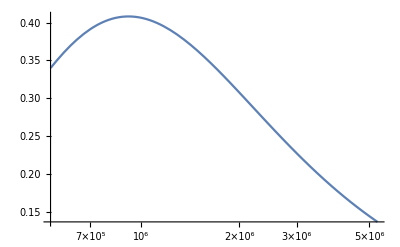

```mathematica
LogLinearPlot[FI, {w, w0, 10*w0}]
```

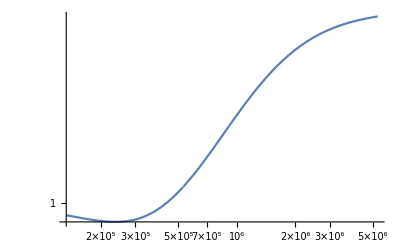

```mathematica
LogLogPlot[G, {w, w0/4, 10*w0}]
```